# Quantum Mechanics and Hydrogen Atoms

## Plots, Wavefunctions, and Probability Clouds

Physics 230: Final Presentation

Aaron Jenkins and Daniel Manning

Brigham Young University

4/18/2026

## Quantum Numbers

### Angular Momentum in Quantum Mechanics

In Uncertainty.nb, we explored the idea that an electron’s position and momentum cannot be precisely known simultaneously. This disproves the Bohr model assumption that electrons orbit at fixed radii from the nucleus, but then that begs the question, where do electrons orbit? How can we describe the orbit of an electron, given the constraints of uncertainty?

To do so, we’ll need to add some additional known quantities to the energy level n; most notably, the angular momentum of an electron. Quantum angular momentum is weird, since it depends on both the radius and the momentum, and those are subject to uncertainty relations. The component of angular momentum is not well defined--instead, we have to specify a total magnitude and a component along a given direction. We use two additional quantum numbers to specify angular momentum: l and m_l.

l is the angular momentum quantum number, which sets the magnitude of the angular momentum. l is nonnegative and has to be less than n. The magnitude of L, the angular momentum, is given by L=(l*(l+1))^1/2.
m_l is the magnetic quantum number, which sets the component along the z direction. The rule for m_l is that |m_l|<l.

A valid set of quantum numbers would be n=3, l=1, m_l=-1. These three are typically expressed in a set, like (3, 1, -1). The following graphs show the basic idea of l and m_l, for l=2 and

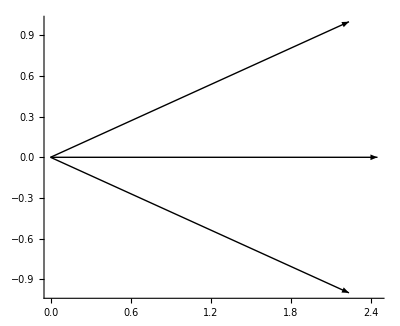

```mathematica
AngularMomentum2DPlot[l_,ml_]:=Module[{},
If[Abs[ml]>l,False,
L=Sqrt[l*(l+1)];
Graphics[Arrow[{{0,0},{Sqrt[L^2-ml^2],ml}}],Axes->True]]
]
Show[AngularMomentum2DPlot[2,-1],AngularMomentum2DPlot[2,1], AngularMomentum2DPlot[2,0]]
```

These plots are 2D, and thus are a little misleading. In reality, the electron could be anywhere on the cone formed by rotating the arrow around the z axis (the y-axis of a 2D plot).

```mathematica
(*This code is not finalized. I need to figure out how to make the code vary with L and ml*)
AngularMomentum3DPlot[l_,ml_]:=Module[{},
L=Sqrt[l*(l+1)];
Plot3D[Sqrt[x^2+y^2],{x,-l,l},{y,-l,l}]
]
AngularMomentum3DPlot[1,1]
```

-Graphics3D-